SetDelayed::write: Tag Real in 1.5[x_] is Protected.

-2.25994+2.49054 x

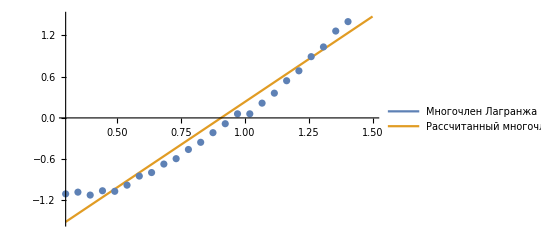

Сумма квадратов отклонений: Abs[-1.51278-1.5[0.3]]^2+Abs[-1.39323-1.5[0.348]]^2+Abs[-1.27369-1.5[0.396]]^2+Abs[-1.15414-1.5[0.444]]^2+Abs[-1.03459-1.5[0.492]]^2+Abs[-0.915049-1.5[0.54]]^2+Abs[-0.795503-1.5[0.588]]^2+Abs[-0.675957-1.5[0.636]]^2+Abs[-0.556412-1.5[0.684]]^2+Abs[-0.436866-1.5[0.732]]^2+Abs[-0.31732-1.5[0.78]]^2+Abs[-0.197774-1.5[0.828]]^2+Abs[-0.0782284-1.5[0.876]]^2+Abs[0.0413174-1.5[0.924]]^2+Abs[0.160863-1.5[0.972]]^2+Abs[0.280409-1.5[1.02]]^2+Abs[0.399955-1.5[1.068]]^2+Abs[0.519501-1.5[1.116]]^2+Abs[0.639046-1.5[1.164]]^2+Abs[0.758592-1.5[1.212]]^2+Abs[0.878138-1.5[1.26]]^2+Abs[0.997684-1.5[1.308]]^2+Abs[1.11723-1.5[1.356]]^2+Abs[1.23678-1.5[1.404]]^2+Abs[1.35632-1.5[1.452]]^2+Abs[1.47587-1.5[1.5]]^2

```mathematica
data = {{0.3,-1.10525},{0.348,-1.07996},{0.396,-1.1225},{0.444,-1.05986},{0.492,-1.06783},{0.54,-0.978257},{0.588,-0.846209},{0.636,-0.794931},{0.684,-0.671395},{0.732,-0.593028},{0.78,-0.459459},{0.828,-0.354877},{0.876,-0.214726},{0.924,-0.0844691},{0.972,0.0593841},
{1.02,0.0593841},{1.068,0.215},{1.116,0.360097},{1.164,0.540909},{1.212,0.685119},{1.26,0.891074},{1.308,1.03252},{1.356,1.26364},
{1.404,1.40065},{1.452,1.65703},{1.5,1.7881}};
n=Length[data]-1;
h=data[[2,1]]-data[[1,1]];
f[x_]:=-7.524199172381958*^10+2.57713246480314*^12 x-4.188311296076594*^13 x^2+4.299937177599049*^14 x^3-3.1321775419846655*^15 x^4+1.7235733740892938*^16 x^5-7.4483622785153*^16 x^6+2.5941218650870694*^17 x^7-7.414300450293256*^17 x^8+1.761556341572748*^18 x^9-3.5112063263108966*^18 x^10+5.908941362500788*^18 x^11-8.429833483988242*^18 x^12+1.021597759189182*^19 x^13-1.0519156707901133*^19 x^14+9.187624272859203*^18 x^15-6.782054545782033*^18 x^16+4.20602614983245*^18 x^17-2.1723279682784033*^18 x^18+9.22788735251155*^17 x^19-3.167583631823541*^17 x^20+8.56503219533247*^16 x^21-1.7556328697361016*^16 x^22+2.563192860985139*^15 x^23-2.374152551164155*^14 x^24+1.0483284654470762*^13 x^25 ;

Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data[[i+1,1]];
ydata[i]=data[[i+1,1]];
];
(*найдём апроксмимрующий многочлен 1-го порядка*)
koefs=FindFit[data,a*x+b,{a,b},x];
y=a*x+b/.koefs
g[x_]:=-2.2599393083333323+2.4905375263532763 x;
gr3:=Plot[{f[x],g[x]},{x,xdata[0],xdata[n]},
PlotLegends->{"Многочлен Лагранжа", "Рассчитанный многочлен 1-ой степени"}]
gr2:=ListPlot[data]
Show[{gr3,gr2}]
sumq = 0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print["Сумма квадратов отклонений: ",sumq];
```